# Rapport projekt 1

Bashar Jamal Pati, bjpati@kth.se
Mohamad Abou Helal, mohamaah@kth.se

## 3. Problem

Lös nedanstående problem. Problemets lösning och resultat skall innehålla visualisering där det är relevant.

### Polynomekvation

Hitta lösningarna till polynomekvationen: x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

```mathematica
f[x_]=x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20
```

20-(148 x)/3-(107 x^2)/3+(25 x^3)/3+(23 x^4)/3+x^5

```mathematica
{x1,x2,x3,x4,x5}=x/.Solve[f[x]==0,x]
```

{-5,-3,-2,1/3,2}

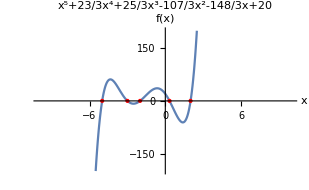

```mathematica
Plot[f[x],{x,-6,4},PlotRange->{{-10,10},{-200,200}},AxesLabel->{"x","f(x)"},PlotLabel->"x^5+23/3x^4+25/3x^3-107/3x^2-148/3x+20", Epilog->{PointSize[Medium],Red,Point[{{x1,f[x1]},{x2,f[x2]},{x3,f[x3]},{x4,f[x4]},{x5,f[x5]}}]}]
```

### Olikhet

Lös uppgift 9 och 10 i filen Algebraiska likheter och olikheter med hjälp av Mathematica. I de fall det är lämpligt illustrera lösningsområdet grafiskt.

Uppgift9 : Lös följande olikheter i domänen av alla reella tal:

```mathematica
x+2>6 x^2
```

x+2>6 x^2

```mathematica
Reduce[x+2>6 x^2,x]
```

-1/2<x<2/3

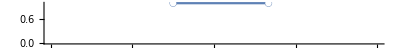

```mathematica
NumberLinePlot[6 x^2<x+2,{x,-2,2}]
```

```mathematica
Clear[x]
```

```mathematica
(x+1)/((2 x+3) (x-2))≥0
```

(x+1)/((x-2) (2 x+3))≥0

```mathematica
Reduce[(x+1)/((2 x+3) (x-2))≥0,x]
```

-3/2<x≤-1∨x>2

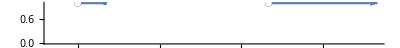

```mathematica
NumberLinePlot[(x+1)/((2 x+3) (x-2))≥0,{x,-2,4}]
```

```mathematica
Clear[x]
```

```mathematica
(x^2-5)/(x-1)≤-1
```

(x^2-5)/(x-1)≤-1

```mathematica
Reduce[(x^2-5)/(x-1)≤-1,x]
```

x≤-3∨1<x≤2

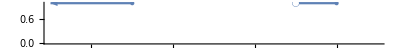

```mathematica
NumberLinePlot[(x^2-5)/(x-1)≤-1,{x,-5,3}]
```

```mathematica
Clear[x]
```

```mathematica
-√(x^2+9)≥2 √x+4
```

-√(x^2+9)≥2 √x+4

```mathematica
Reduce[-√(x^2+9)≥2 √x+4,x]
```

False

```mathematica
Clear[x]
```

```mathematica
√(3 x+3)≥√x+1
```

√(3 x+3)≥√x+1

```mathematica
Reduce[√(3 x+3)≥√x+1,x]
```

x≥0

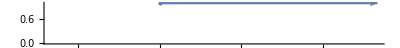

```mathematica
NumberLinePlot[√(3 x+3)≥√x+1,{x,-2,4}]
```

```mathematica
Clear[x]
```

```mathematica
Uppgift 10:Bestämsanningsmängder till följande predikater i domänen av alla reella tal:
```

```mathematica
x^3<1∧x^2-x-6≥0
```

x^3<1∧x^2-x-6≥0

```mathematica
Reduce[x^3<1∧x^2-x-6≥0,x]
```

x≤-2

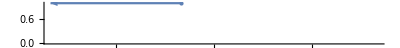

```mathematica
NumberLinePlot[x^3<1∧x^2-x-6≥0,{x,-4,1}]
```

```mathematica
Clear[x]
```

```mathematica
(2 x-1) (x-3) (2 x-5)==0∧√(x^2-x-2)≥2
```

(x-3) (2 x-5) (2 x-1)==0∧√(x^2-x-2)≥2

```mathematica
Reduce[(x-3) (2 x-5) (2 x-1)==0∧√(x^2-x-2)≥2,x]
```

x==3

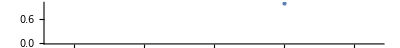

```mathematica
NumberLinePlot[(2 x-1) (x-3) (2 x-5)==0∧√(x^2-x-2)≥2,{x,-2,5}]
```

```mathematica
Clear[x]
```

```mathematica
√(x^2-x-2)≥√x∧x^2-1≥0
```

√(x^2-x-2)≥√x∧x^2-1≥0

```mathematica
Reduce[√(x^2-x-2)≥√x∧x^2-1≥0,x]
```

x≥√3+1

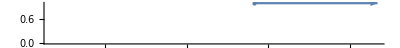

```mathematica
NumberLinePlot[√(x^2-x-2)≥√x∧x^2-1≥0,{x,-1,5}]
```

### Binomisk ekvation

```mathematica
Quit[]
```

Finn lösningen till ekvationen z^6=-3+3i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

```mathematica
Z=z/.Solve[z^6==-3+3ⅈ]//N
```

{-1.1755-0.486907 ⅈ,1.1755+0.486907 ⅈ,-0.166075-1.26146 ⅈ,0.166075+1.26146 ⅈ,1.00942-0.774557 ⅈ,-1.00942+0.774557 ⅈ}

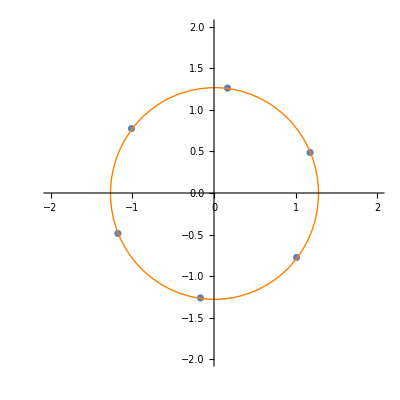

```mathematica
ComplexListPlot[Z,Epilog->{RGBColor[1, 0.501961,0],Circle[{0,0},Abs[Z⟦1⟧]]},PlotRange->{{-2,2},{-2,2}}]
```

### Logik

Lös uppgift 1b  i filen Logik med hjälp av Mathematica.

```mathematica
Quit[]
```

```mathematica
√2∈Reals∧¬√2∈Rationals
```

True

```mathematica
1/2∈Integers||1/2∈Rationals
```

True

```mathematica
¬(-4∈Integers∧-4≥0)⇒¬-4∈Integers
```

False

```mathematica
5/2∈Rationals⧦5/2∈Reals
```

True

### Ekvationslösning och grafer

En D’Artagnan jagas av Richeliue. Båda rider så snabbt de kan. D’Artagnan rider med en hastighet av 42 km/h och Richeliue med 57 km/h. Richeliue är 60 meter efter D’Artagnan och det är 250 meter till stadsporten där D’Artagnan kan komma undan. Bestäm om Richeliue hinner i kapp D’Artagnan och i så fall vilken tidpunkt och sträcka innan stadsporten det sker. Illustrera tidsförloppet grafiskt på lämpligt sätt.

```mathematica
Quit[]
```

```mathematica
v1=42/3.6
```

11.6667

```mathematica
v2=57/3.6
```

15.8333

```mathematica
s1(t_):=t v1+60
```

```mathematica
s2(t_):=t v2
```

```mathematica
d=t/.Solve[s1(t)==s2(t),t]
```

{14.4}

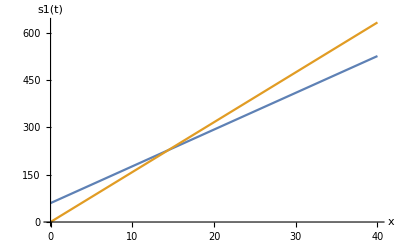

```mathematica
Plot[{s1[t],s2[t]},{t,0,40},AxesLabel->{"x", "s1(t)"}]
```

```mathematica
t0=t/.Solve[s1(t)==s2(t),t]
```

{14.4}

```mathematica
s1(t0)
```

{228.}

```mathematica
s2(t0)
```

{228.}